```mathematica
D[s[w[k]-b[l]*r[k],R],l]
```

-r[k] b'[l] s^(1,0)[-b[l] r[k]+w[k],R]

```mathematica
Limit[(1-α)*k^α-b*(α*k^(α-1)-1-n)/(1+n)-g,k-> ∞,Assumptions->{α>0,α<1}]
```

∞

```mathematica
pts=Reap[Plot[{c1[k],c2[k]},{k,0,.2},EvaluationMonitor:>Sow[{k,c1[k]}]]][[-1,1]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
pts2=Reap[Plot[{c1[k],c2[k]},{k,0,.2},EvaluationMonitor:>Sow[{k,c2[k]}]]][[-1,1]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
func[k_,b_,g_]:=β/((1+n)*(1+β))*((1-α)*k^α-b*(α*k^(α-1)-1-n)/(1+n)-g)-b/(1+n)/.{β-> 0.9,n-> .1,α-> 0.3}
```

```mathematica
c1[k_]:=β/((1+n)*(1+β))*((1-α)*k^α-b*(α*k^(α-1)-1-n)/(1+n)-g)-b/.{β-> 0.9,n-> .1,α-> 0.3,b->0.05,g->0.04}
```

```mathematica
c2[k_]:=β/((1+n)*(1+β))*((1-α)*k^α-b*(α*k^(α-1)-1-n)/(1+n)-g)-b/.{β-> 0.9,n-> .1,α-> 0.3,b->0.1,g->0.04}
```

```mathematica
Limit[c1[k]-c2[k],k-> 0]
```

Indeterminate

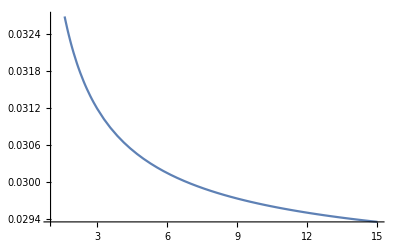

```mathematica
Plot[c1[k]-c2[k],{k,1,15}]
```

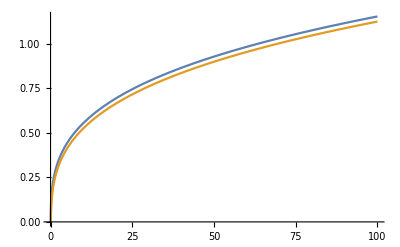

```mathematica
Plot[{c1[k],c2[k]},{k,0,100}]
```

```mathematica
FullSimplify[D[c,k,k]]
```

0

```mathematica
-(k^(-2+α) (b+k+k n) (-1+α) α β)/((1+n)^2 (1+β))
```

```mathematica
Limit[-(k^(-2+α) (-1+α) α β)/((1+n)^2 (1+β)),k-> ∞,Assumptions->{α>0,α<1}]
```

0

```mathematica
Limit[c,k-> ∞,Direction->"FromAbove",Assumptions->{α>0,α<1}]
```

c

```mathematica
ss0=k/.NSolve[k==func[k,0.02,0],k]
```

{0.153517,0.0105513}

```mathematica
ss1=k/.NSolve[k==func[k,0,0],k]
```

{0.180298,0.}

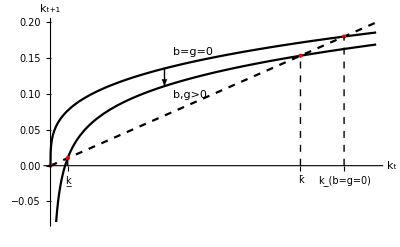

```mathematica
pl=Plot[{k,func[k,0,0],func[k,0.02,0]},{k,0,0.2},PlotStyle->{{Dashed,Black},Black,Black},Epilog->{
{Red,PointSize[Large],Point[{#,func[#,0,0]}]&/@ss1},
{PointSize[Large],Red,Point[{#,func[#,0.02,0]}]&/@ss0},
{Dashed,Line[{{#,0},{#,func[#,0.02,0]}}]&/@ss0},{Dashed,Line[{{#,0},{#,func[#,0,0]}}]&/@ss1},
{Arrowheads[Small],Arrow[{{0.07,func[0.07,0,0]},{0.07,func[0.07,0.02,0]}}]},
Text["b,g>0",{0.07+0.005,(func[0.07,0,0]+func[0.07,0.02,0])/2-0.025},Left],Text["b=g=0",{0.07+0.005,(func[0.07,0,0]+func[0.07,0.02,0])/2+0.035},Left]
},Ticks-> {{{ss0[[2]],UnderBar["k"]},{ss0[[1]],OverBar["k"]},{ss1[[1]],Subscript["k","b=g=0"]}},None},AxesLabel->{Subscript["k","t"],Subscript["k","t+1"]}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/taxes.png",pl]
```

/home/eric/eric-roca.github.io/static/img/olg/taxes.png